```mathematica
HexBasis = {{1,0},{1/2,Sqrt[3]/2}}
```

{{1,0},{1/2,(√3)/2}}

```mathematica
MakeGrid[size_] := Flatten[Table[{x,y}, {x, -size, size}, {y, -size, size}] ,1]
```

```mathematica
GraphicsRow[{
Graphics[{
{PointSize[Medium], Point /@ MakeGrid[5]},
Circle[{0,0}, #] & /@ Union[ Norm /@ MakeGrid[4]]
}],Graphics[{
{PointSize[Medium], Point /@ (MakeGrid[7].HexBasis)},
Circle[{0,0}, #] & /@ Union[ Norm /@ (MakeGrid[4].HexBasis)]
}]
}]
```

-Graphics-

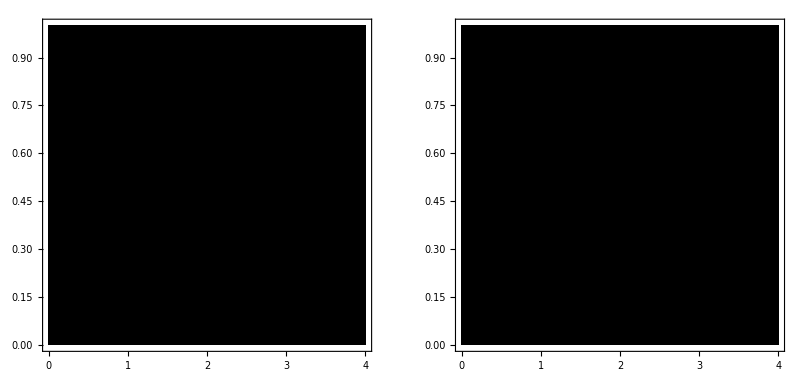

```mathematica
GraphicsRow[{
DensityPlot[
Abs[Subtract[
x,
First@Nearest[Union[Norm/@MakeGrid[4]],x]
]], 
{x,0, 4}, {y, 0, 1},MaxRecursion-> 4, PlotTheme->"Monochrome"],
DensityPlot[
Abs[Subtract[
x,
First@Nearest[Union[Norm/@(MakeGrid[4].HexBasis)],x]
]], 
{x,0, 4}, {y, 0, 1},MaxRecursion-> 4, PlotTheme->"Monochrome"]
}]
```

```mathematica
DrawMandala[range_] := Module[
{
squaregrid = MakeGrid[Round@range],
shellcount = CountsBy[ MakeGrid[Round@range], Norm] ,
density =1 / (Sqrt[range] * (100 + range))
},
Graphics[{
PointSize[density*(shellcount[Norm[#]])],
Point[#]
} & /@ squaregrid,
PlotRange-> 4range /5
]]
```

```mathematica
DrawHexMandala[range_] := Module[
{
squaregrid = MakeGrid[Round@range].HexBasis,
shellcount = CountsBy[ MakeGrid[Round@range].HexBasis, Norm] ,
density =1 / (Sqrt[range] * (180 + range))
},
Graphics[{
PointSize[density*(shellcount[Norm[#]])],
Point[#]
} & /@ squaregrid,
PlotRange->  range
]]
```

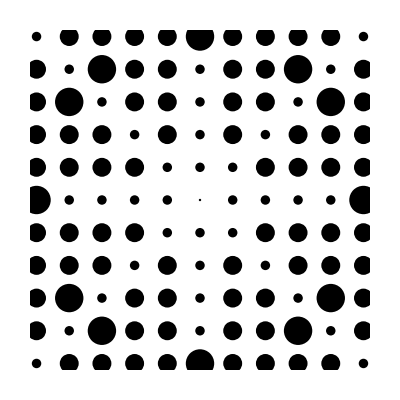
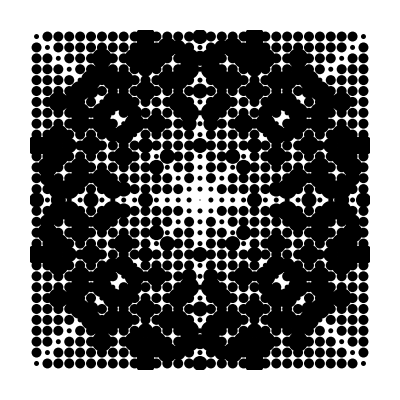
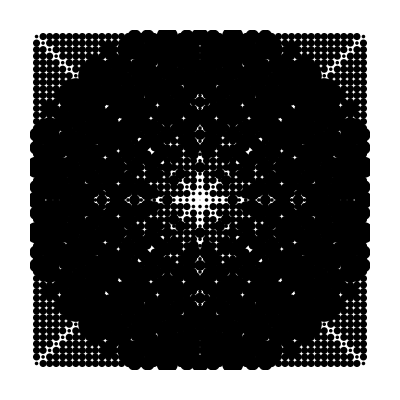
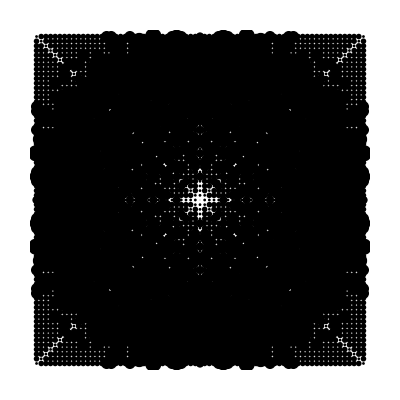
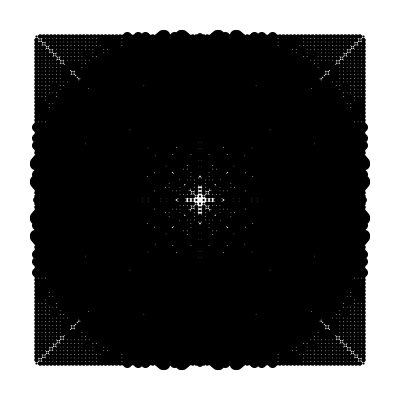

```mathematica
Table[DrawMandala[n], {n,5, 50, 10}]
```

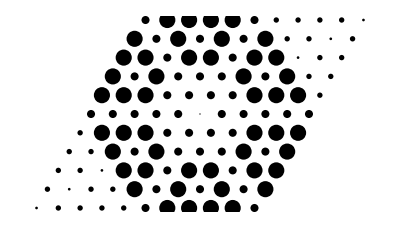
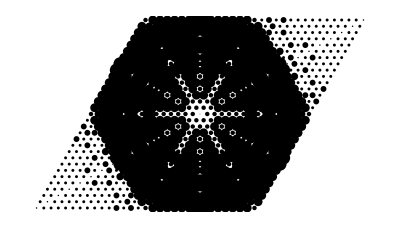
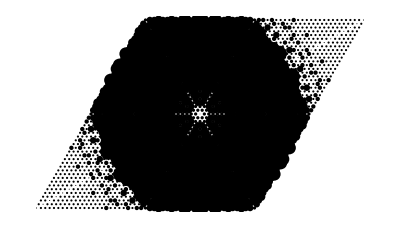
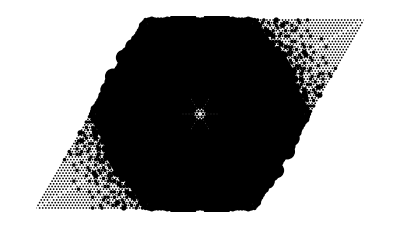
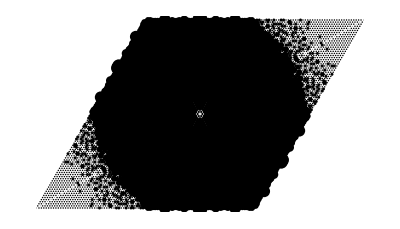

```mathematica
Table[DrawHexMandala[n], {n,5, 50, 10}]
```